{1<->2,1<->10,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10}

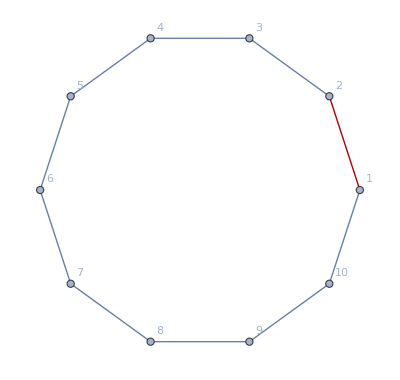
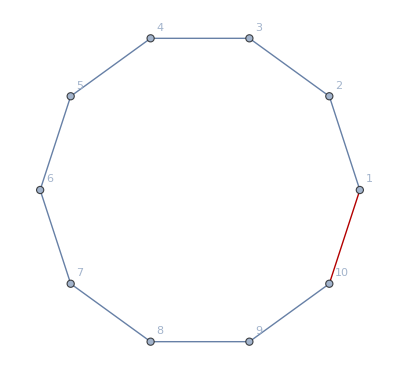
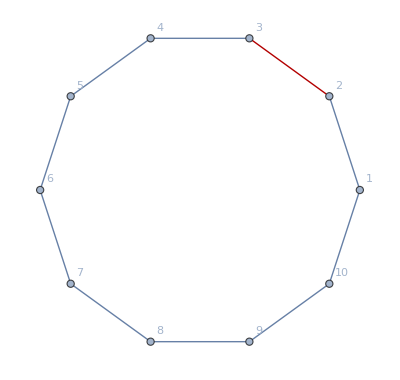
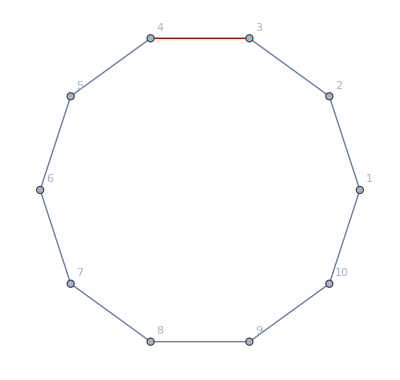
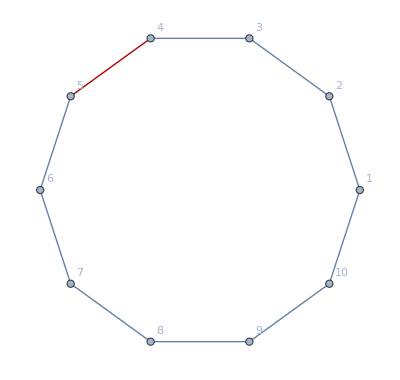

(0 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1
1 | 0 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2
2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 4 | 3
3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 4
4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5
5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4
4 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3
3 | 4 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2
2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 0 | 1
1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 0)

{0.0625,Null}

```mathematica
coords=Table[{Cos[θ],Sin[θ]},{θ,0,0.9*2π,0.1*2π}];
g=EdgeAdd[GridGraph[{10},VertexLabels->"Name",VertexCoordinates->coords],1<->10];(*RandomGraph[{10,10},VertexCoordinates->coords]*)
es=EdgeList[g]
Table[HighlightGraph[g,eh],{eh,es⟦1;;5⟧}]
gd=GraphDistanceMatrix[g];
gd//MatrixForm
(* It does not take long to compute distances in graphs *)
Timing[g2=RandomGraph[{1000,2000}];
gd2=GraphDistanceMatrix[g2];]
```

{{{1,2}→1,{1,10}→1,{2,1}→1,{2,3}→1,{3,2}→1,{3,4}→1,{4,3}→1,{4,5}→1,{5,4}→1,{5,6}→1,{6,5}→1,{6,7}→1,{7,6}→1,{7,8}→1,{8,7}→1,{8,9}→1,{9,8}→1,{9,10}→1,{10,1}→1,{10,9}→1},{{1,3}→2,{1,9}→2,{2,4}→2,{2,10}→2,{3,1}→2,{3,5}→2,{4,2}→2,{4,6}→2,{5,3}→2,{5,7}→2,{6,4}→2,{6,8}→2,{7,5}→2,{7,9}→2,{8,6}→2,{8,10}→2,{9,1}→2,{9,7}→2,{10,2}→2,{10,8}→2},{{1,4}→3,{1,8}→3,{2,5}→3,{2,9}→3,{3,6}→3,{3,10}→3,{4,1}→3,{4,7}→3,{5,2}→3,{5,8}→3,{6,3}→3,{6,9}→3,{7,4}→3,{7,10}→3,{8,1}→3,{8,5}→3,{9,2}→3,{9,6}→3,{10,3}→3,{10,7}→3},{{1,5}→4,{1,7}→4,{2,6}→4,{2,8}→4,{3,7}→4,{3,9}→4,{4,8}→4,{4,10}→4,{5,1}→4,{5,9}→4,{6,2}→4,{6,10}→4,{7,1}→4,{7,3}→4,{8,2}→4,{8,4}→4,{9,3}→4,{9,5}→4,{10,4}→4,{10,6}→4},{{1,6}→5,{2,7}→5,{3,8}→5,{4,9}→5,{5,10}→5,{6,1}→5,{7,2}→5,{8,3}→5,{9,4}→5,{10,5}→5}}

{{1,{{1,2},{1,10},{2,1},{2,3},{3,2},{3,4},{4,3},{4,5},{5,4},{5,6},{6,5},{6,7},{7,6},{7,8},{8,7},{8,9},{9,8},{9,10},{10,1},{10,9}}},{2,{{1,3},{1,9},{2,4},{2,10},{3,1},{3,5},{4,2},{4,6},{5,3},{5,7},{6,4},{6,8},{7,5},{7,9},{8,6},{8,10},{9,1},{9,7},{10,2},{10,8}}},{3,{{1,4},{1,8},{2,5},{2,9},{3,6},{3,10},{4,1},{4,7},{5,2},{5,8},{6,3},{6,9},{7,4},{7,10},{8,1},{8,5},{9,2},{9,6},{10,3},{10,7}}},{4,{{1,5},{1,7},{2,6},{2,8},{3,7},{3,9},{4,8},{4,10},{5,1},{5,9},{6,2},{6,10},{7,1},{7,3},{8,2},{8,4},{9,3},{9,5},{10,4},{10,6}}},{5,{{1,6},{2,7},{3,8},{4,9},{5,10},{6,1},{7,2},{8,3},{9,4},{10,5}}}}

{1<->3,1<->9,2<->4,2<->10,3<->5,4<->6,5<->7,6<->8,7<->9,8<->10}

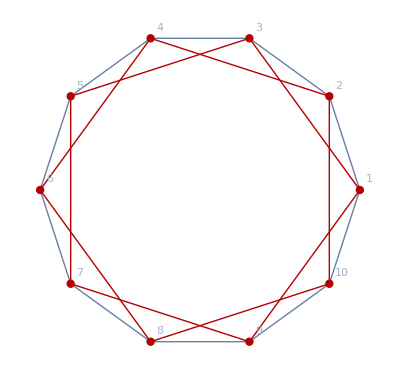
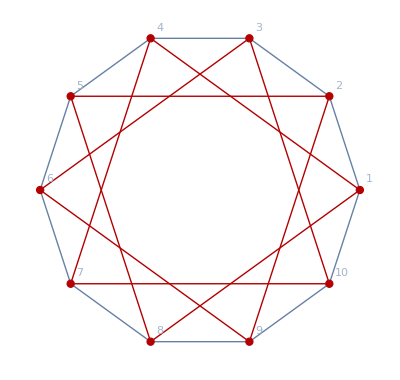
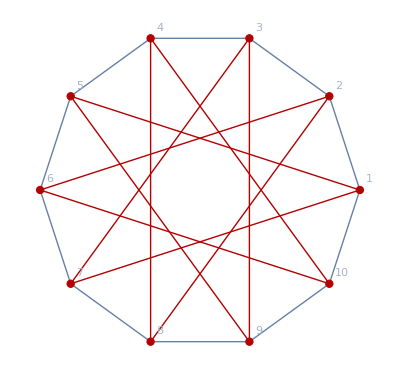
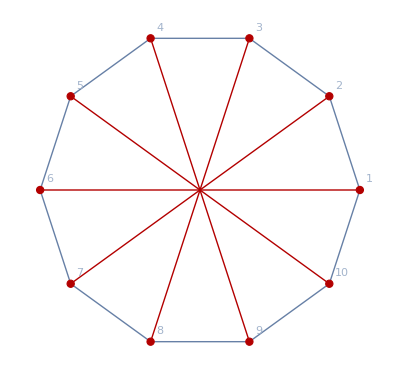
{{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-}}

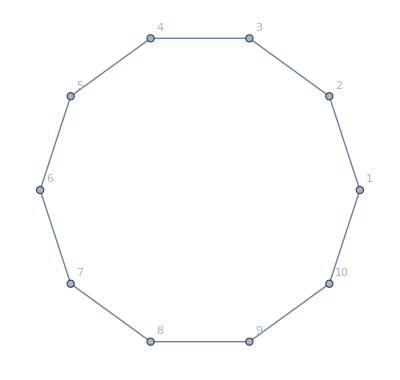
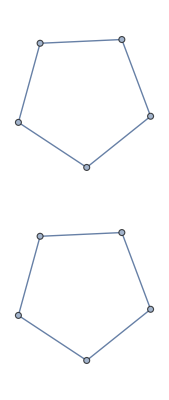
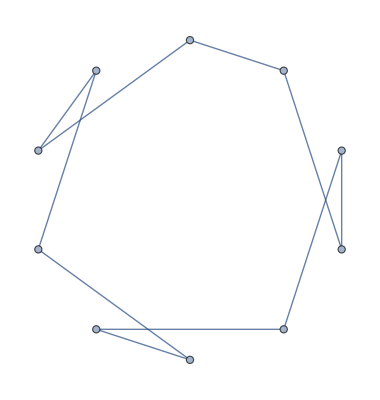
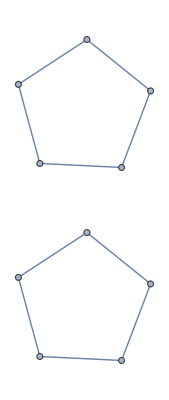
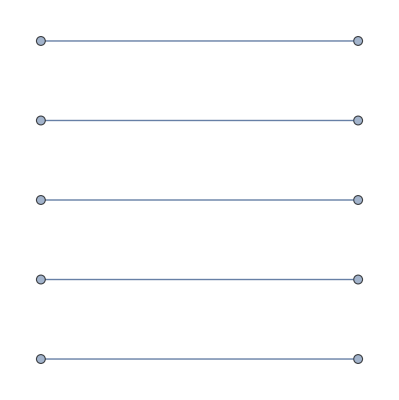
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-}}

```mathematica
(* Gather site-shuffle operations by the number of site-hoppings they would require  *)
ConnByHops=Gather[ArrayRules[SparseArray[gd]]⟦1;;-2⟧,#2⟦2⟧==#1⟦2⟧&](*Arrayrules operates on a sparse array and returns a list of position->value of the sparse array, and then use Gather to pick out all shufflings with the same distance*)
ConnByHops=Sort[Partition[Riffle[ConnByHops⟦All,1,2⟧,ConnByHops⟦All,All,1⟧],2],#1⟦1⟧<#2⟦1⟧&]
(*The list of shuffling operator->distance is rearranged so that the first element of each row is the distance and the rest are operators*)
s=2;
ConnByHops⟦s,2⟧;
Map[UndirectedEdge[#⟦1⟧,#⟦2⟧]&,ConnByHops⟦s,2⟧];
Tally[Map[UndirectedEdge[#⟦1⟧,#⟦2⟧]&,ConnByHops⟦s,2⟧],Sort[#1]==Sort[#2]&]⟦All,1⟧(*This picks out all the elements with distance 2 and sort them by the first site. Each element represent an shuffling operator and its inversion*)
Table[gs=Graph[Tally[Map[UndirectedEdge[#⟦1⟧,#⟦2⟧]&,ConnByHops⟦s,2⟧],Sort[#1]==Sort[#2]&]⟦All,1⟧];
{s,HighlightGraph[GraphUnion[g,gs,VertexLabels->"Name",VertexCoordinates->coords],gs]},{s,2,Dimensions[ConnByHops]⟦1⟧}](*This forms a table of {distance, graphs of shufflings and the shuffling paths are highlighted}*)
ConnByHopsG=Join[{{1,g}},Table[{ConnByHops⟦s,1⟧,Graph[Tally[Map[UndirectedEdge[#⟦1⟧,#⟦2⟧]&,ConnByHops⟦s,2⟧],Sort[#1]==Sort[#2]&]⟦All,1⟧]},{s,2,Dimensions[ConnByHops]⟦1⟧}]](*?*)
```

```mathematica
(*Join[{List},Table[Select[ConnByHops,#⟦1⟧==s&]⟦1,2⟧,{s,{2,1}}],{1}]
Apply[Outer,Join[{List},Table[Select[ConnByHops,#⟦1⟧==s&]⟦1,2⟧,{s,{2,1}}],{1}]](*test in order to understand this code*)*)
```

```mathematica
(*ip={{1,1,1},{2,1}};
shuffles=Table[Flatten[
Apply[Outer,Join[{List},Table[Select[ConnByHops,#⟦1⟧==s&]⟦1,2⟧,{s,p}],{1}]]
,Length[p]-1],{p,ip}];
shuffles=Flatten[shuffles,1]*)
```

```mathematica
(* Now break down for each order M in t, all possible partitions of shuffle-distances allowed *)
maxTorder=4;  (* Generating shuffling paths to order 5 requires 1.5s, sorting another 62s, represents 3 x10^6 states in 10-site 1D chain, requires 1.4GB of memory to store results *)
Timing[
allshuffs=Table[
ip=IntegerPartitions[M,All,ConnByHopsG⟦All,1⟧];(*List of all combinations of allowed distances adding up to M, e.g. for M=3. ip={{1,1,1},{2,1}},refer to Help->IntegerPartitions->Scope->3*)
shuffles=Table[Flatten[
Apply[Outer,Join[{List},Table[Select[ConnByHops,#⟦1⟧==s&]⟦1,2⟧,{s,p}],{1}]](*This select function choose the group of shuffling operators with distance s to look into, p goes through all the combinations in list ip, and s goes through all steps in list p. Table function build lists of all the paths, in which each row correspond to a step; Apply function take the outer product of each rows, then shuffles are all the paths, first level refer to a list of distances of each step, each level contains all the paths; Finally shuffles is flattened so that it's a list of all possible paths in a certain level of tunneling*)
,Length[p]-1]
,{p,ip}];
d=Dimensions[shuffles];
shuffles=Flatten[shuffles,1](*after this flatten, each element of the first level is a path; So allshuffle is a list of shuffles with different total shuffling distances M*)
,{M,1,maxTorder}];
]
(* Now regroup the shuffle index pairs into groups of raising and lowering indices, each group sorted - can view this as normalordering of ((a^*)_j1 Subscript[a, i1](a^*)_j2 Subscript[a, i2](a^*)_j3 Subscript[a, i3] into (a^*)_j1(a^*)_j2(a^*)_j3 Subscript[a, i1] Subscript[a, i2] Subscript[a, i3] with site indices is and js sorted into definite order *)
Timing[
allshuffsNormRaising=Map[Sort,allshuffs⟦All,All,All,1⟧,{2}];
allshuffsNormLowering=Map[Sort,allshuffs⟦All,All,All,2⟧,{2}];
]
(* Sorting is expensive - we do it 1) to decide if we have by the method above created duplicate states and remove them. 2) to more rapidly determine matrix elements of tunneling operator - by the method above we are sure that only states in levels n-1, n+1 can be connected to states in n - this is true sorted or not.  But to find states within that, we need to find shuffle sequences which differ by a single shuffle. it would be better if our generation method did this automatically eliminating the shuffle problem.     *)
```

{0.04688,Null}

{0.23438,Null}

```mathematica
Dimensions[allshuffsNormRaising⟦maxTorder⟧]
```

{168820}

```mathematica
i1=3;
i2=590;
allshuffs⟦i1,i2⟧
{allshuffs⟦i1,i2⟧⟦All,1⟧,allshuffs⟦i1,i2⟧⟦All,2⟧}
{allshuffs⟦All,All,All,1⟧⟦i1,i2⟧,allshuffs⟦All,All,All,2⟧⟦i1,i2⟧}

{Map[Sort,allshuffs⟦All,All,All,1⟧,{2}]⟦i1,i2⟧,Map[Sort,allshuffs⟦All,All,All,2⟧,{2}]⟦i1,i2⟧}
```

{{1,2},{5,4},{5,6}}

{{1,5,5},{2,4,6}}

{{1,5,5},{2,4,6}}

{{1,5,5},{2,4,6}}

```mathematica
gam=GraphAutomorphismGroup[g]
```

PermutationGroup[{Cycles[{{2,10},{3,9},{4,8},{5,7}}],Cycles[{{1,2,3,4,5,6,7,8,9,10}}]}]

```mathematica
GroupOrder[gam]
GroupElements[gam]
Length[GroupElements[gam]]
```

20

{Cycles[{}],Cycles[{{2,10},{3,9},{4,8},{5,7}}],Cycles[{{1,2},{3,10},{4,9},{5,8},{6,7}}],Cycles[{{1,2,3,4,5,6,7,8,9,10}}],Cycles[{{1,3},{4,10},{5,9},{6,8}}],Cycles[{{1,3,5,7,9},{2,4,6,8,10}}],Cycles[{{1,4},{2,3},{5,10},{6,9},{7,8}}],Cycles[{{1,4,7,10,3,6,9,2,5,8}}],Cycles[{{1,5},{2,4},{6,10},{7,9}}],Cycles[{{1,5,9,3,7},{2,6,10,4,8}}],Cycles[{{1,6},{2,5},{3,4},{7,10},{8,9}}],Cycles[{{1,6},{2,7},{3,8},{4,9},{5,10}}],Cycles[{{1,7},{2,6},{3,5},{8,10}}],Cycles[{{1,7,3,9,5},{2,8,4,10,6}}],Cycles[{{1,8},{2,7},{3,6},{4,5},{9,10}}],Cycles[{{1,8,5,2,9,6,3,10,7,4}}],Cycles[{{1,9},{2,8},{3,7},{4,6}}],Cycles[{{1,9,7,5,3},{2,10,8,6,4}}],Cycles[{{1,10,9,8,7,6,5,4,3,2}}],Cycles[{{1,10},{2,9},{3,8},{4,7},{5,6}}]}

20

```mathematica
PermutationReplace[{3,7},Cycles[{{1,2,3,4,5,6,7,8,9,10}}]]
```

{10,1}

```mathematica
GroupOrbits[gam,VertexList[VertexAdd[g,11]]]
```

{{1,2,3,4,5,6,7,8,9,10},{11}}

```mathematica
ge=VertexAdd[g,{11,12}];
ge=EdgeAdd[g,{11<->12}];
VertexList[ge]
Complement[VertexList[ge],PermutationSupport[GraphAutomorphismGroup[ge]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

{}

```mathematica
(* All inequivalent choices of a vertex *)
v1s=GroupOrbits[GraphAutomorphismGroup[ge],VertexList[ge]]⟦All,1⟧;
(* All inequivalent choices of a first edge *)
e1s=Map[List,GroupOrbits[GraphAutomorphismGroup[ge],Flatten[Table[Outer[UndirectedEdge,{v1},AdjacencyList[ge,v1]],{v1,v1s}]]]⟦All,1⟧]
(*Table[GroupOrbits[GraphAutomorphismGroup[ge],Outer[UndirectedEdge,{v1},AdjacencyList[ge,v1]]],{v1,v1s}]⟦All,All,1⟧*)
(* All inequivalent choices of a first two-step *)
e1v3=GroupOrbits[GraphAutomorphismGroup[ge],Flatten[Outer[List,e1s,VertexList[ge]],2]]⟦All,1⟧;
e2=Flatten[Map[Outer[List,{#⟦1;;-2⟧},Outer[UndirectedEdge,{#⟦-1⟧},AdjacencyList[ge,#⟦-1⟧]]]&,e1v3],4]
e2=GroupOrbits[GraphAutomorphismGroup[ge],e2]⟦All,1⟧;
(* All inequivalent choices of three-steps *)
e2v5=GroupOrbits[GraphAutomorphismGroup[ge],Flatten[Outer[Append,e2,VertexList[ge],1],1]]⟦All,1⟧;
e3=Flatten[Map[Outer[Append,{#⟦1;;-2⟧},Flatten[Outer[UndirectedEdge,{#⟦-1⟧},AdjacencyList[ge,#⟦-1⟧]]],1]&,e2v5],2];
e3=GroupOrbits[GraphAutomorphismGroup[ge],e3]⟦All,1⟧;
e3⟦1;;30⟧
(* Note the growth of elements - there are only ~470 inequivalent 3-steps for the 10-site chain, instead of O(8000) in a full listing - there are 9800 inequivalent 4-steps, compared to O(2 x10^5), so there is some improvement over blind ignorance of symmetry but not so much! *)
```

{{1<->2},{11<->12}}

{{1<->2,1<->2},{1<->2,1<->10},{1<->2,2<->1},{1<->2,2<->3},{1<->2,3<->2},{1<->2,3<->4},{1<->2,4<->3},{1<->2,4<->5},{1<->2,5<->4},{1<->2,5<->6},{1<->2,6<->5},{1<->2,6<->7},{1<->2,7<->6},{1<->2,7<->8},{1<->2,8<->7},{1<->2,8<->9},{1<->2,9<->8},{1<->2,9<->10},{1<->2,10<->1},{1<->2,10<->9},{1<->2,11<->12},{11<->12,1<->2},{11<->12,1<->10},{11<->12,11<->12},{11<->12,12<->11}}

{{1<->2,1<->2,1<->2},{1<->2,1<->2,1<->10},{1<->2,1<->2,2<->1},{1<->2,1<->2,2<->3},{1<->2,1<->2,3<->2},{1<->2,1<->2,3<->4},{1<->2,1<->2,4<->3},{1<->2,1<->2,4<->5},{1<->2,1<->2,5<->4},{1<->2,1<->2,5<->6},{1<->2,1<->2,6<->5},{1<->2,1<->2,6<->7},{1<->2,1<->2,7<->6},{1<->2,1<->2,7<->8},{1<->2,1<->2,8<->7},{1<->2,1<->2,8<->9},{1<->2,1<->2,9<->8},{1<->2,1<->2,9<->10},{1<->2,1<->2,10<->1},{1<->2,1<->2,10<->9},{1<->2,1<->2,11<->12},{1<->2,1<->10,1<->2},{1<->2,1<->10,1<->10},{1<->2,1<->10,2<->1},{1<->2,1<->10,2<->3},{1<->2,1<->10,3<->2},{1<->2,1<->10,3<->4},{1<->2,1<->10,4<->3},{1<->2,1<->10,4<->5},{1<->2,1<->10,5<->4}}

```mathematica
(* Now we need a generic iterative procedure to take e1 -> e2 -> e3 -> e4 ->... *)
iteratestep[graph_,graphAM_,en_]:=Module[{},
env=GroupOrbits[graphAM,Flatten[Outer[Append,en,VertexList[graph],1],1]]⟦All,1⟧;
enp1=Flatten[Map[Outer[Append,{#⟦1;;-2⟧},Flatten[Outer[UndirectedEdge,{#⟦-1⟧},AdjacencyList[graph,#⟦-1⟧]]],1]&,env],2];
enp1=GroupOrbits[GraphAutomorphismGroup[ge],enp1]⟦All,1⟧;
enp1
]
```

```mathematica
Timing[e3I=iteratestep[ge,GraphAutomorphismGroup[ge],e2];]
e3I==e3
Timing[e4I=iteratestep[ge,GraphAutomorphismGroup[ge],e3];]
```

{2.24641,Null}

True

{53.14954,Null}

```mathematica
e4I⟦1;;10⟧
Partition[Riffle[e4I⟦1;;10,All,1⟧,e4I⟦1;;10,All,2⟧],2]
Map[Tally,Partition[Riffle[e4I⟦1;;10,All,1⟧,e4I⟦1;;10,All,2⟧],2],{2}]
Length[e4I]
```

{{1<->2,1<->2,1<->2,1<->2},{1<->2,1<->2,1<->2,1<->10},{1<->2,1<->2,1<->2,2<->1},{1<->2,1<->2,1<->2,2<->3},{1<->2,1<->2,1<->2,3<->2},{1<->2,1<->2,1<->2,3<->4},{1<->2,1<->2,1<->2,4<->3},{1<->2,1<->2,1<->2,4<->5},{1<->2,1<->2,1<->2,5<->4},{1<->2,1<->2,1<->2,5<->6}}

{{{1,1,1,1},{2,2,2,2}},{{1,1,1,1},{2,2,2,10}},{{1,1,1,2},{2,2,2,1}},{{1,1,1,2},{2,2,2,3}},{{1,1,1,3},{2,2,2,2}},{{1,1,1,3},{2,2,2,4}},{{1,1,1,4},{2,2,2,3}},{{1,1,1,4},{2,2,2,5}},{{1,1,1,5},{2,2,2,4}},{{1,1,1,5},{2,2,2,6}}}

{{{{1,4}},{{2,4}}},{{{1,4}},{{2,3},{10,1}}},{{{1,3},{2,1}},{{2,3},{1,1}}},{{{1,3},{2,1}},{{2,3},{3,1}}},{{{1,3},{3,1}},{{2,4}}},{{{1,3},{3,1}},{{2,3},{4,1}}},{{{1,3},{4,1}},{{2,3},{3,1}}},{{{1,3},{4,1}},{{2,3},{5,1}}},{{{1,3},{5,1}},{{2,3},{4,1}}},{{{1,3},{5,1}},{{2,3},{6,1}}}}

9864